Goal:  Use the previously acquired universal indictor training data to infer pH in amphiphile solutions with unknown pH.

## Import Training Data

This is essentially identical to the data loading in 2023.07.20_ expanded_dataset.nb

Use a local copy of the data provided by Christelle Ekosso on 20 July 2023, via Slack/Google Drive;

```mathematica
SeedRandom[1841]; (*set a random seed for training/test set generation for replicability*)
SetDirectory@NotebookDirectory[];
<<"src/platereader.wl"
```

```mathematica
(*some trickiness to merge the files provided in an appropriate way...*)
spectra=With[
{sortedPlateFileNames =SortBy[StringTake[#,-10]&]@FileNames["data/2023_07_20_PH_Indicator/*.txt"]},
Normal@Map[Flatten]@Merge[Join]@Map[importPlateReaderFile]@sortedPlateFileNames];

measuredpH = With[
{dataRows=Join[Range[4,11],Range[16,23],Range[27,34],Range[38,45],Range[49,56],Range[61,68]]},
Import[
"data/2023_07_20_PH_Indicator/20230720 pH Indicator Plates.xlsx",
{"Data",2,dataRows,2;;13},
"EmptyField"->Missing []]//Flatten];

(* handle an extraneous sample in Plate 4, as noted in the data integrity log; this throws off our analysis of the triplicate measurement statistics; for simplicity we will exclude it from all processes *)
measuredpH =measuredpH// With[
{plate = 4, row = 6, col = 10 (*4:F10*)},
With [ 
{position = (plate-1)*96+(row-1)*12+col},
ReplacePart[ position->Missing[]]]];

wavelengths=spectra[[All,1]];
```

```mathematica
(*get data into a list of {spectra}-> pH values*)
normalizeSpectrum[l_?VectorQ]:=Normalize[#,Total]&@(l-Min[l])

output[spectrum_List,pH_?NumericQ]:=(normalizeSpectrum[spectrum]->pH);
output[_,_]:=Nothing;  (*if there is not a Numeric pH value, then drop this entry from both sets *)

(*in the order they are presented...no need to sort by pH*)
data =MapThread[output, {Transpose[spectra[[All,2,All]]],measuredpH}];
```

## Train Model

Based on previous work (2023.07.20_expanded_dataset.nb), Gradient Boosted Trees trained on the complete (non-dimensional reduced) dataset had the best performance for predicting pH.

```mathematica
model = Predict[data,
Method->"GradientBoostedTrees",
PerformanceGoal->"Quality"];

Information[model]
```

Predictor information
Data type | NumericalVector (××41)
Standard deviation | 0.61 ± 0.32
Method | GradientBoostedTrees
Single evaluation time | 5.95 ms/example
Batch evaluation speed | 21.8 examples/ms
Loss | 2.74 ± 1.4
Model memory | 419. kB
Training examples used | 393 examples
Training time | 4.44 s
 |

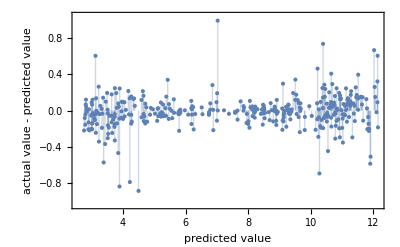

```mathematica
PredictorMeasurements[model,data,"ResidualPlot"]
```

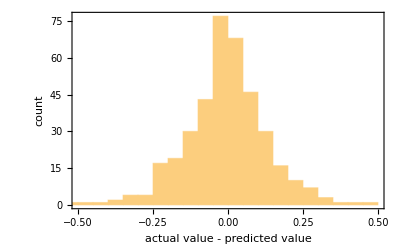

```mathematica
PredictorMeasurements[model,data,"ResidualHistogram"]
```

```mathematica
Mean@Abs@PredictorMeasurements[model,data,"Residuals"]
```

0.1189

## Make Inferences

Load data
Apply model to data
Write outputs to XLSX file
???
Profit!